Define dX=mAXdt+mΣdW, call mV the asymptotic covariance matrix of X, mR the time covariance matrix and mr the time correlation matrix

```mathematica
mΣ = {{σ1,c},{0,σ2}}
```

{{σ1,c},{0,σ2}}

```mathematica
mA = {{-λ1,0},{0,-λ2}}
```

{{-λ1,0},{0,-λ2}}

```mathematica
Eigenvalues[mA]
```

{-λ1,-λ2}

```mathematica
mV = Array[v,{2,2}]
```

{{v[1,1],v[1,2]},{v[2,1],v[2,2]}}

```mathematica
assum={σ1>0,σ2>0,λ1>0,λ2>0,c1>0,c2>0,d1>0,d2>0,σ>0,c>0,d>0,ϵ>0,δ>0,s>0}
```

{σ1>0,σ2>0,λ1>0,λ2>0,c1>0,c2>0,d1>0,d2>0,σ>0,c>0,d>0,ϵ>0,δ>0,s>0}

```mathematica
values = {σ1->0.1,σ2->2,λ2->1,c1->0.1,c2->0.1,d1->0.1,d2->0.1,σ->1,c->1,d->0.1,ϵ->1,δ->5,s->0}
```

{σ1→0.1,σ2→2,λ2→1,c1→0.1,c2→0.1,d1→0.1,d2→0.1,σ→1,c→1,d→0.1,ϵ→1,δ→5,s→0}

```mathematica
λmin=0
```

0

```mathematica
λmax=4
```

4

```mathematica
plotpoints=100
```

100

```mathematica
solV=Simplify[Solve[mA.mV+mV.Transpose[mA]==-ϵ^2*mΣ.Transpose[mΣ],Flatten[mV]]][[1]]
```

{v[1,1]→(ϵ^2 (c^2+σ1^2))/(2 λ1),v[1,2]→(c ϵ^2 σ2)/(λ1+λ2),v[2,1]→(c ϵ^2 σ2)/(λ1+λ2),v[2,2]→(ϵ^2 σ2^2)/(2 λ2)}

```mathematica
mR[τ_]=Simplify[MatrixExp[τ*mA].mV/.solV,Assumptions->assum]
```

{{(ⅇ^(-λ1 τ) ϵ^2 (c^2+σ1^2))/(2 λ1),(c ⅇ^(-λ1 τ) ϵ^2 σ2)/(λ1+λ2)},{(c ⅇ^(-λ2 τ) ϵ^2 σ2)/(λ1+λ2),(ⅇ^(-λ2 τ) ϵ^2 σ2^2)/(2 λ2)}}

```mathematica
mr[τ_]=Simplify[{{mR[τ][[1,1]]/mR[0][[1,1]],mR[τ][[1,2]]/Sqrt[mR[0][[1,1]]*mR[0][[2,2]]]},{mR[τ][[2,1]]/Sqrt[mR[0][[1,1]]*mR[0][[2,2]]],mR[τ][[2,2]]/mR[0][[2,2]]}},Assumptions->assum]
```

{{ⅇ^(-λ1 τ),(2 c ⅇ^(-λ1 τ) √((λ1 λ2)/(c^2+σ1^2)))/(λ1+λ2)},{(2 c ⅇ^(-λ2 τ) √((λ1 λ2)/(c^2+σ1^2)))/(λ1+λ2),ⅇ^(-λ2 τ)}}

```mathematica
Simplify[Series[mr[τ][[1,1]]/.{c1->ϵ,c2->ϵ,d1->ϵ,d2->ϵ,c->ϵ,d->ϵ},{ϵ,0,2}],Assumptions->assum]
```

ⅇ^(-λ1 τ)

```mathematica
Limit[ⅇ^(-λ1 τ),{λ1->0},Direction->"FromAbove",Assumptions->{σ1>0,σ2>0,λ1>0,λ2>0,c1>0,c2>0,d1>0,d2>0}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

```mathematica
tvar[β_,λ1_]=Cos[β]^2*mR[0][[1,1]]+Sin[β]^2*mR[0][[2,2]]+Cos[β]*Sin[β]*mR[0][[1,2]]+Sin[β]*Cos[β]*mR[0][[2,1]]
```

(ϵ^2 (c^2+σ1^2) Cos[β]^2)/(2 λ1)+(2 c ϵ^2 σ2 Cos[β] Sin[β])/(λ1+λ2)+(ϵ^2 σ2^2 Sin[β]^2)/(2 λ2)

```mathematica
tdvar[β_,λ1_]=-D[tvar[β,λ1],λ1]
```

(ϵ^2 (c^2+σ1^2) Cos[β]^2)/(2 λ1^2)+(2 c ϵ^2 σ2 Cos[β] Sin[β])/(λ1+λ2)^2

```mathematica
D[tdvar[β,λ2],β]/.β->π/2
```

-(c ϵ^2 σ2)/(2 λ2^2)

```mathematica
tac1[β_,λ1_]=(Cos[β]^2*mR[1][[1,1]]+Sin[β]^2*mR[1][[2,2]]+Cos[β]*Sin[β]*mR[1][[1,2]]+Sin[β]*Cos[β]*mR[1][[2,1]])/tvar[β,λ1]
```

((ⅇ^-λ1 ϵ^2 (c^2+σ1^2) Cos[β]^2)/(2 λ1)+(c ⅇ^-λ1 ϵ^2 σ2 Cos[β] Sin[β])/(λ1+λ2)+(c ⅇ^-λ2 ϵ^2 σ2 Cos[β] Sin[β])/(λ1+λ2)+(ⅇ^-λ2 ϵ^2 σ2^2 Sin[β]^2)/(2 λ2))/((ϵ^2 (c^2+σ1^2) Cos[β]^2)/(2 λ1)+(2 c ϵ^2 σ2 Cos[β] Sin[β])/(λ1+λ2)+(ϵ^2 σ2^2 Sin[β]^2)/(2 λ2))

```mathematica
tdac1[β_,λ1_]=Simplify[-D[tac1[β,λ1],λ1]]
```

(Cos[β] ((ⅇ^-λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+ⅇ^-λ1 λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+2 c ⅇ^-λ1 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ2 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ1 λ1^2 (λ1+λ2) σ2 Sin[β]) (λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+4 c λ1 λ2 σ2 Cos[β] Sin[β]+λ1 (λ1+λ2) σ2^2 Sin[β]^2)-ⅇ^(-λ1-λ2) ((λ1+λ2)^2 (c^2+σ1^2) Cos[β]+4 c λ1^2 σ2 Sin[β]) (ⅇ^λ2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+λ1 σ2 Sin[β] (2 c (ⅇ^λ1+ⅇ^λ2) λ2 Cos[β]+ⅇ^λ1 (λ1+λ2) σ2 Sin[β]))))/(λ1^3 λ2 (λ1+λ2)^3 (((c^2+σ1^2) Cos[β]^2)/λ1+(4 c σ2 Cos[β] Sin[β])/(λ1+λ2)+(σ2^2 Sin[β]^2)/λ2)^2)

```mathematica
Simplify[D[tdac1[β,λ2],β]/.β->π/2]
```

-(c ⅇ^-λ2)/σ2

```mathematica
angle=-Pi/4
```

-π/4

```mathematica
var[β_,λ1_]=tvar[β,λ1]/.values
```

(0.505 Cos[β]^2)/λ1+(4 Cos[β] Sin[β])/(1+λ1)+2 Sin[β]^2

```mathematica
ac1[β_,λ1_]=tac1[β,λ1]/.values
```

((0.505 ⅇ^-λ1 Cos[β]^2)/λ1+(2 Cos[β] Sin[β])/(ⅇ (1+λ1))+(2 ⅇ^-λ1 Cos[β] Sin[β])/(1+λ1)+(2 Sin[β]^2)/ⅇ)/((0.505 Cos[β]^2)/λ1+(4 Cos[β] Sin[β])/(1+λ1)+2 Sin[β]^2)

```mathematica
dvar[β_,λ1_]=tdvar[β,λ1]/.values
```

(0.505 Cos[β]^2)/λ1^2+(4 Cos[β] Sin[β])/(1+λ1)^2

```mathematica
dac1[β_,λ1_]=tdac1[β,λ1]/.values
```

(Cos[β] ((1.01 ⅇ^-λ1 (1+λ1)^2 Cos[β]+1.01 ⅇ^-λ1 λ1 (1+λ1)^2 Cos[β]+(4 λ1^2 Sin[β])/ⅇ+4 ⅇ^-λ1 λ1^2 Sin[β]+4 ⅇ^-λ1 λ1^2 (1+λ1) Sin[β]) (1.01 (1+λ1) Cos[β]^2+8 λ1 Cos[β] Sin[β]+4 λ1 (1+λ1) Sin[β]^2)-ⅇ^(-1-λ1) (1.01 (1+λ1)^2 Cos[β]+8 λ1^2 Sin[β]) (2.74546 (1+λ1) Cos[β]^2+2 λ1 Sin[β] (2 (ⅇ+ⅇ^λ1) Cos[β]+2 ⅇ^λ1 (1+λ1) Sin[β]))))/(λ1^3 (1+λ1)^3 ((1.01 Cos[β]^2)/λ1+(8 Cos[β] Sin[β])/(1+λ1)+4 Sin[β]^2)^2)

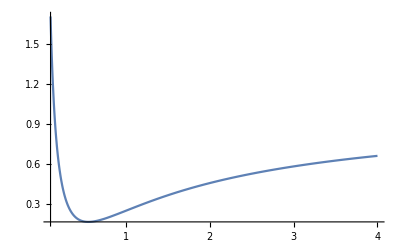

```mathematica
Plot[var[angle,x],{x,λmin+0.1,λmax},PlotRange->All]
```

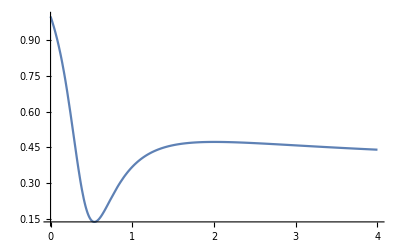

```mathematica
Plot[ac1[angle,x],{x,λmin,λmax},PlotRange->All]
```

```mathematica
Show[{Plot3D[var[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin],Element[{x,y},Region[Disk[]]],PlotRange->{0,3},ColorFunction->Function[{x,y},If[dvar[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin]>0,Red,Blue]],ColorFunctionScaling->False,PlotPoints->plotpoints],ParametricPlot3D[{Cos[angle]*r,Sin[angle]*r,var[angle,r*(λmax-λmin)+λmin]},{r,0,1},PlotStyle->{Green,Thickness->0.015},PlotPoints->plotpoints],ParametricPlot3D[{2/λmax*Cos[β],2/λmax*Sin[β],var[β,2]},{β,0,2*π},PlotStyle->{Black,Thickness->0.01},PlotPoints->plotpoints]},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Show[{Plot3D[ac1[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin],Element[{x,y},Region[Disk[]]],PlotRange->All,ColorFunction->Function[{x,y},If[dac1[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin]>0,Red,Blue]],ColorFunctionScaling->False,PlotPoints->plotpoints],ParametricPlot3D[{Cos[angle]*r,Sin[angle]*r,ac1[angle,r*(λmax-λmin)+λmin]},{r,0,1},PlotStyle->{Green,Thickness->0.015},PlotPoints->plotpoints],ParametricPlot3D[{2/λmax*Cos[β],2/λmax*Sin[β],ac1[β,2]},{β,0,2*π},PlotStyle->{Black,Thickness->0.01},PlotPoints->plotpoints]},Boxed->False,Axes->False]
```

-Graphics3D-

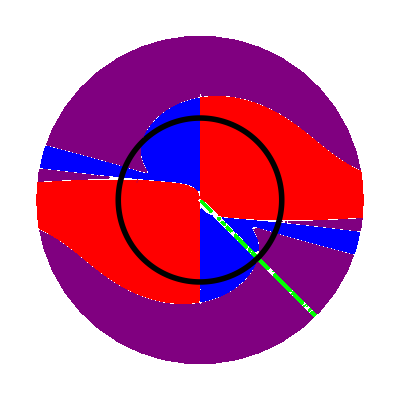

```mathematica
Show[{DensityPlot[If[Or[And[ArcTan[x,y]<angle+0.013/Sqrt[(x^2+y^2)],  ArcTan[x,y]>angle-0.013/Sqrt[(x^2+y^2)]],And[ArcTan[x,y]<angle+0.013/Sqrt[(x^2+y^2)]-2*Pi,  ArcTan[x,y]>angle-0.013/Sqrt[(x^2+y^2)]-2*Pi]],0.2,If[dac1[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin]>0,If[dvar[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin]>0,0,0.5],If[dvar[ArcTan[x,y],(λmax-λmin)*Sqrt[(x^2+y^2)]+λmin]>0,0.5,1]]],Element[{x,y},Region[Disk[]]],ColorFunction->Function[x,Which[x==0,Red,x==0.5,Purple,x==1,Blue,x==0.2,Green]],ColorFunctionScaling->False,PlotPoints->plotpoints],PolarPlot[2/λmax,{θ,0,2 Pi},PlotStyle->{Black,Thickness->0.01}]},Frame->False,Axes->False]
```

### Prove that close to Pi/2 and for a specific lambda1, both Var and AC(1) decrease

```mathematica
tdvar[Pi/2,λ1]
```

0

```mathematica
tddvar[β_,λ1_]=D[tdvar[β,λ1],β]
```

(2 c ϵ^2 σ2 Cos[β]^2)/(λ1+λ2)^2-(ϵ^2 (c^2+σ1^2) Cos[β] Sin[β])/λ1^2-(2 c ϵ^2 σ2 Sin[β]^2)/(λ1+λ2)^2

```mathematica
tddvar[Pi/2,λ1]
```

-(2 c ϵ^2 σ2)/(λ1+λ2)^2

If wlog c>0, then all β in some range (π/2,β2) and all λ1 have the property that the variance decreases as λ1 decreases towards 0. Similarly analyse the AC(1):

```mathematica
tdac1[Pi/2,λ1]
```

0

```mathematica
tddac1[β_,λ1_]=D[tdac1[β,λ1],β]
```

(Cos[β] ((ⅇ^-λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+ⅇ^-λ1 λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+2 c ⅇ^-λ1 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ2 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ1 λ1^2 (λ1+λ2) σ2 Sin[β]) (4 c λ1 λ2 σ2 Cos[β]^2-2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β] Sin[β]+2 λ1 (λ1+λ2) σ2^2 Cos[β] Sin[β]-4 c λ1 λ2 σ2 Sin[β]^2)+(2 c ⅇ^-λ1 λ1^2 σ2 Cos[β]+2 c ⅇ^-λ2 λ1^2 σ2 Cos[β]+2 c ⅇ^-λ1 λ1^2 (λ1+λ2) σ2 Cos[β]-ⅇ^-λ1 (λ1+λ2)^2 (c^2+σ1^2) Sin[β]-ⅇ^-λ1 λ1 (λ1+λ2)^2 (c^2+σ1^2) Sin[β]) (λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+4 c λ1 λ2 σ2 Cos[β] Sin[β]+λ1 (λ1+λ2) σ2^2 Sin[β]^2)-ⅇ^(-λ1-λ2) ((λ1+λ2)^2 (c^2+σ1^2) Cos[β]+4 c λ1^2 σ2 Sin[β]) (-2 ⅇ^λ2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β] Sin[β]+λ1 σ2 Sin[β] (ⅇ^λ1 (λ1+λ2) σ2 Cos[β]-2 c (ⅇ^λ1+ⅇ^λ2) λ2 Sin[β])+λ1 σ2 Cos[β] (2 c (ⅇ^λ1+ⅇ^λ2) λ2 Cos[β]+ⅇ^λ1 (λ1+λ2) σ2 Sin[β]))-ⅇ^(-λ1-λ2) (4 c λ1^2 σ2 Cos[β]-(λ1+λ2)^2 (c^2+σ1^2) Sin[β]) (ⅇ^λ2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+λ1 σ2 Sin[β] (2 c (ⅇ^λ1+ⅇ^λ2) λ2 Cos[β]+ⅇ^λ1 (λ1+λ2) σ2 Sin[β]))))/(λ1^3 λ2 (λ1+λ2)^3 (((c^2+σ1^2) Cos[β]^2)/λ1+(4 c σ2 Cos[β] Sin[β])/(λ1+λ2)+(σ2^2 Sin[β]^2)/λ2)^2)-(2 Cos[β] ((4 c σ2 Cos[β]^2)/(λ1+λ2)-(2 (c^2+σ1^2) Cos[β] Sin[β])/λ1+(2 σ2^2 Cos[β] Sin[β])/λ2-(4 c σ2 Sin[β]^2)/(λ1+λ2)) ((ⅇ^-λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+ⅇ^-λ1 λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+2 c ⅇ^-λ1 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ2 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ1 λ1^2 (λ1+λ2) σ2 Sin[β]) (λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+4 c λ1 λ2 σ2 Cos[β] Sin[β]+λ1 (λ1+λ2) σ2^2 Sin[β]^2)-ⅇ^(-λ1-λ2) ((λ1+λ2)^2 (c^2+σ1^2) Cos[β]+4 c λ1^2 σ2 Sin[β]) (ⅇ^λ2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+λ1 σ2 Sin[β] (2 c (ⅇ^λ1+ⅇ^λ2) λ2 Cos[β]+ⅇ^λ1 (λ1+λ2) σ2 Sin[β]))))/(λ1^3 λ2 (λ1+λ2)^3 (((c^2+σ1^2) Cos[β]^2)/λ1+(4 c σ2 Cos[β] Sin[β])/(λ1+λ2)+(σ2^2 Sin[β]^2)/λ2)^3)-(Sin[β] ((ⅇ^-λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+ⅇ^-λ1 λ1 (λ1+λ2)^2 (c^2+σ1^2) Cos[β]+2 c ⅇ^-λ1 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ2 λ1^2 σ2 Sin[β]+2 c ⅇ^-λ1 λ1^2 (λ1+λ2) σ2 Sin[β]) (λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+4 c λ1 λ2 σ2 Cos[β] Sin[β]+λ1 (λ1+λ2) σ2^2 Sin[β]^2)-ⅇ^(-λ1-λ2) ((λ1+λ2)^2 (c^2+σ1^2) Cos[β]+4 c λ1^2 σ2 Sin[β]) (ⅇ^λ2 λ2 (λ1+λ2) (c^2+σ1^2) Cos[β]^2+λ1 σ2 Sin[β] (2 c (ⅇ^λ1+ⅇ^λ2) λ2 Cos[β]+ⅇ^λ1 (λ1+λ2) σ2 Sin[β]))))/(λ1^3 λ2 (λ1+λ2)^3 (((c^2+σ1^2) Cos[β]^2)/λ1+(4 c σ2 Cos[β] Sin[β])/(λ1+λ2)+(σ2^2 Sin[β]^2)/λ2)^2)

```mathematica
Simplify[tddac1[Pi/2,λ2]]
```

-(c ⅇ^-λ2)/σ2

If wlog c>0, then all β in some range (π/2,β2) and all λ1 in (λ2-δ,λ2+δ) have the property that the variance decreases as λ1 decreases towards 0.